```mathematica
"definição do retângulo"
a=1
b=1
```

definição do retângulo

1

1

```mathematica
"definição da base utilizada"
φ[x_,y_,n_,m_]=Sin[π*n(x/a)]Sin[π*m(y/b)]
nM=2
mM=2
Base[x_,y_]=Table[φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM],{i,0,nM*mM-1}]
```

definição da base utilizada

Sin[n π x] Sin[m π y]

2

2

{Sin[π x] Sin[π y],Sin[2 π x] Sin[π y],Sin[π x] Sin[2 π y],Sin[2 π x] Sin[2 π y]}

```mathematica
"definição da matriz A"
A[k_] = Table[NIntegrate[φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM]Laplacian[φ[x,y,1+Mod[j,nM],1+(j-Mod[j,nM])/mM],{x,y}],{y,0,b},{x,0,a},AccuracyGoal->6]+k^2 NIntegrate[φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM]φ[x,y,1+Mod[j,nM],1+(j-Mod[j,nM])/mM],{y,0,b},{x,0,a},AccuracyGoal->6],{i,0,nM*mM-1},{j,0,nM*mM-1}]
A[k] // MatrixForm
```

definição da matriz A

{{-4.9348+0.25 k^2,1.72591×10^-15-1.30794×10^-17 k^2,1.80326×10^-15-1.67065×10^-17 k^2,-1.54753×10^-16+2.41802×10^-18 k^2},{5.54783×10^-16-1.30794×10^-17 k^2,-12.337+0.25 k^2,3.63177×10^-31+2.41802×10^-18 k^2,1.95129×10^-15-2.78673×10^-17 k^2},{5.35445×10^-16-1.67065×10^-17 k^2,3.63177×10^-31+2.41802×10^-18 k^2,-12.337+0.25 k^2,2.57027×10^-15-2.30307×10^-17 k^2},{-3.86883×10^-17+2.41802×10^-18 k^2,1.14216×10^-15-2.78673×10^-17 k^2,1.14223×10^-15-2.30307×10^-17 k^2,-19.7392+0.25 k^2}}

(-4.9348+0.25 k^2 | 1.72591×10^-15-1.30794×10^-17 k^2 | 1.80326×10^-15-1.67065×10^-17 k^2 | -1.54753×10^-16+2.41802×10^-18 k^2
5.54783×10^-16-1.30794×10^-17 k^2 | -12.337+0.25 k^2 | 3.63177×10^-31+2.41802×10^-18 k^2 | 1.95129×10^-15-2.78673×10^-17 k^2
5.35445×10^-16-1.67065×10^-17 k^2 | 3.63177×10^-31+2.41802×10^-18 k^2 | -12.337+0.25 k^2 | 2.57027×10^-15-2.30307×10^-17 k^2
-3.86883×10^-17+2.41802×10^-18 k^2 | 1.14216×10^-15-2.78673×10^-17 k^2 | 1.14223×10^-15-2.30307×10^-17 k^2 | -19.7392+0.25 k^2)

```mathematica
"autovalores obtidos numericamente"
NSolve[Det[A[k]]== 0 && k ≥ 0,k]
```

autovalores obtidos numericamente

{{k→4.44288},{k→7.02481},{k→7.02481},{k→8.88577}}

```mathematica
"autofunções(para um dado autovalor ka) obtidas numericamente: id é um indice de degenerescencia"
ka=8.885765876316736
Vc[ka]=NullSpace[A[ka]]
id=1
v=Vc[ka][[id]]
ϕ[x_,y_]=Base[x,y].v
```

autofunções(para um dado autovalor ka) obtidas numericamente: id é um indice de degenerescencia

8.88577

{{-2.44292×10^-18,-5.92858×10^-18,-9.1975×10^-17,1.}}

1

{-2.44292×10^-18,-5.92858×10^-18,-9.1975×10^-17,1.}

-2.44292×10^-18 Sin[π x] Sin[π y]-5.92858×10^-18 Sin[2 π x] Sin[π y]-9.1975×10^-17 Sin[π x] Sin[2 π y]+1. Sin[2 π x] Sin[2 π y]

```mathematica
"esboço da autofunção obtida"
Plot3D[ϕ[x,y],{x,0,a},{y,0,b}]
```

esboço da autofunção obtida

-Graphics3D-

curvas de nível da autofunção

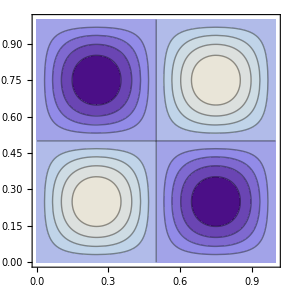

```mathematica
"curvas de nível da autofunção"
ContourPlot[ϕ[x,y],{x,0,a},{y,0,b}]
```